## Initialization

Load packages

```mathematica
$HistoryLength=1;
On@Assert;
(*If package is installed to a non standard dir add it to path just in case*)
With[{pfn=ExpandFileName@FileNameJoin[{NotebookDirectory[],"..",".."}]},
If[!MemberQ[$Path,pfn], PrependTo[$Path,pfn]];
];
Needs["Developer`"]
Needs["DiffusiveDynamics`"]
(*Load the data on paralle Kernels*)

With[{path=$Path},
ParallelEvaluate[
$Path=path;(*add to the path of parallel Kernels*)
$HistoryLength=1;
Needs["Developer`"];
Needs["DiffusiveDynamics`"];
]];
$VerbosePrint=True;

R[α_]:={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};
DDD[Dx_,Dy_]:={{1/Dx^2,0},{0,1/Dy^2}};
D2DMat[Dx_,Dy_,α_]:=N[R[α °].DDD[Dx,Dy].Transpose[R[α °]]];
```

Define diffusion parameters

```mathematica
STEPS=2000000;
STEP=1;
CELLRANGE={1000.,500.};
ModI[x_,halfwidth_]:=Mod[x+halfwidth,2*halfwidth]-halfwidth;
ClearAll[DIFFX,DIFFY,DIFFA];
DIFFX=Compile[{x,y},
5Sin[x/ CELLRANGE[[1]] π] +10];
DIFFY=Compile[{x,y},
5Sin[y/ CELLRANGE[[2]] π] +10];
DIFFA=Compile[{x,y},
(((x/2)/CELLRANGE[[1]])^2+((y/2)/ CELLRANGE[[2]])^2)*180];


TENSOR[x_,y_]:=D2DMat[DIFFX[x,y],DIFFY[x,y],DIFFA[x,y]];
ClearAll[ENERGY]; (*energija v enotah kT*)
energyExp=1-3*Rest@PDF[MultinormalDistribution[{0,0},DiagonalMatrix[(CELLRANGE/4)^2]],{x,y}];
```

```mathematica
ENERGY=Compile[{x,y},Evaluate@energyExp];

KT=1.;
CELL$plots=DiffusionParameters2DPlots[DIFFX,DIFFY,DIFFA,ENERGY,CELLRANGE]
StringForm["STEPS `1`; STEP `2`; KT `3`",STEPS,STEP,KT];
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Generate Data

{0.90205,Null}

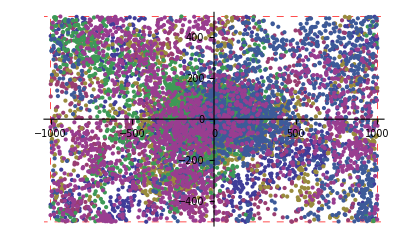

```mathematica
$VerbosePrint = True;
$VerboseLevel = 3;
AbsoluteTiming[
 rw = ParallelGenerateDiffusionTrajectory2D[STEPS=1000000 , DIFFX, DIFFY, DIFFA, ENERGY, KT, STEP, {-CELLRANGE, CELLRANGE}, Verbose -> False,"VerboseLevel"->3, "InitialPositions" -> Automatic, "ProcessCount" -> 6];
 ]


w = {250, 125}*1;(*width of bin*)
w0 = {0, 0}; (*lower left point of bin*)
ListPlot[rw[[All, ;; ;; Ceiling[STEPS/10000], {2, 3}]], PlotRange -> Transpose@{-CELLRANGE, CELLRANGE}, GridLines -> Transpose@{-CELLRANGE, CELLRANGE}, GridLinesStyle -> Directive[Red, Thick, Dashed],
 Epilog -> {Opacity[0], EdgeForm[{Red, Thick}], Rectangle[w0 - w/2, w0 + w/2]}]
```

## Analyze diffusion

Fitted diffusion

```mathematica
w=CELLRANGE/4;
binSpec=Transpose[{-CELLRANGE,CELLRANGE,w}];
strides={1,200};
strides={1,5,7,10, 50,100,400};
```

```mathematica
$VerbosePrint=True;
$VerboseLevel=2;
```

```mathematica
AbsoluteTiming[diffs=GetDiffusionInBins[rw,STEP,binSpec,"CellRange"->{-CELLRANGE,CELLRANGE},"Strides"->strides,"PadSteps"->True,"PadOnlyShort"->True,Parallel->True,"ReturnStepsHistogram"->True,"WarnIfEmpty"->False,"NormalitySignificanceLevel"->.01];]
diffs=DiffusionNormalForm@diffs;
Dimensions@diffs
```

{21.69824,Null}

{64,7,19}

Actual model diffusions

```mathematica
AbsoluteTiming@Short[actualDiffs=GetDiffusionInfoFromParameters[binSpec,STEP,strides,DIFFX,DIFFY,DIFFA,"ReturnStepsHistogram"->True,"Parallel"->True],10]
actualDiffs=DiffusionNormalForm@actualDiffs;
Dimensions@actualDiffs;
```

{5.58132,{«1»}}

## Compare two diffusions

Normalize the diffusion representation

```mathematica
diffs=DiffusionNormalForm@diffs;
actualDiffs=DiffusionNormalForm@actualDiffs;
```

Load/Save diffusions

```mathematica
diffsFileName=NotebookDirectory[]<>"\\Data\\diffs.mx.gz";
actualDiffsfFileName=NotebookDirectory[]<>"\\Data\\actual.diffs.mx.gz";
```

```mathematica
(*Import*)
(*
AbsoluteTiming[diffs=Import[diffsFileName];]
AbsoluteTiming[actualDiffs=Import[actualDiffsfFileName];]
*)
```

```mathematica
Grid
```

```mathematica
(*Export*)
AbsoluteTiming@Export[diffsFileName,diffs]
AbsoluteTiming@Export[actualDiffsfFileName,actualDiffs]
```

```mathematica
Dimensions@actualDiffs
```

Draw tensor representations

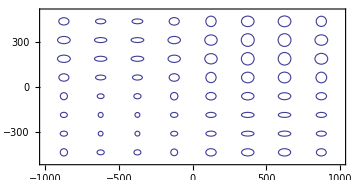

```mathematica
DrawDiffusionTensorRepresentations[diffs[[All,1]],6,Scale->3,"MarkSelectedBin"->False]
```

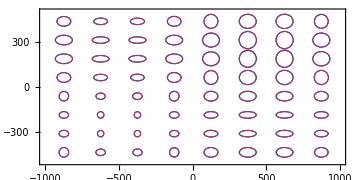

```mathematica
DrawDiffusionTensorRepresentations[{diffs[[All,1]], actualDiffs[[All,1]]},1,Verbose->False,Scale->4]
```

Explore using manipulate

```mathematica
ViewDiffsWithStridePlots[diffs,"Fitted Difussion",PlotStyle->Directive[ColorData[1][2],Thick],SaveDefinitions->False,Verbose->False]
```

```mathematica
ViewDiffsWithStridePlots[actualDiffs,"Actual Diffusion",SaveDefinitions->False,Verbose->False]
```

```mathematica
ViewDiffsWithStridePlots[{diffs,actualDiffs},"Comparison Actual/Fitted",SaveDefinitions->False,Verbose->False]
```

## Misc

```mathematica
(*For easier storage in Git*)
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False];FrontEndTokenExecute["DeleteGeneratedCells"];
(*Auto delete output on close*)
```

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndTokenExecute["DeleteGeneratedCells"]}];
```

```mathematica
CloseKernels[]
```

```mathematica
ViewDiffsWithStridePlots[{nopad,weakpad,pad,actualDiffs},"Comparison Actual/Fitted",SaveDefinitions->False,Verbose->False,"LegendCaptions"->{"nopad","weakpad","pad","actual"}]
```

```mathematica
Export["padcompareSin.mx.gz",{nopad,weakpad,pad,actualDiffs}];//AbsoluteTiming
```

```mathematica
{nopad,weakpad,pad,actualDiffs}=Import@"padcompare.mx.gz";//AbsoluteTiming
```